### Tests

```mathematica
M={{1,0,t1/2,t1/2},{0,-1,-t1/2,-t1/2},{t1/2,-t1/2,1,0},{t1/2,-t1/2,0,-1}};
%//MatrixForm
```

(1 | 0 | t1/2 | t1/2
0 | -1 | -t1/2 | -t1/2
t1/2 | -t1/2 | 1 | 0
t1/2 | -t1/2 | 0 | -1)

```mathematica
es=Series[Eigensystem[M],{t1,0,1}]//Normal
```

{{-1-t1/2,-1+t1/2,1-t1/2,1+t1/2},{{-t1/4,1,t1/4,1},{-t1/4,-1,-t1/4,1},{4/t1+t1/4,1,-4/t1-t1/4,1},{4/t1+t1/4,-1,4/t1+t1/4,1}}}

```mathematica
es={{-1-t1/2,-1+t1/2,1-t1/2,1+t1/2},{{-t1/4,1,t1/4,1},{t1/4,1,t1/4,-1},{1,t1/4,-1,t1/4},{1,-t1/4,1,t1/4}}};
```

```mathematica
pp=1/Sqrt[2] es[[2,4]]
```

{1/(√2),-t1/(4 √2),1/(√2),t1/(4 √2)}

```mathematica
pm=1/Sqrt[2] es[[2,3]]
```

{1/(√2),t1/(4 √2),-1/(√2),t1/(4 √2)}

```mathematica
mp=1/Sqrt[2] es[[2,2]]
```

{t1/(4 √2),1/(√2),t1/(4 √2),-1/(√2)}

```mathematica
mm=1/Sqrt[2] es[[2,1]]
```

{-t1/(4 √2),1/(√2),t1/(4 √2),1/(√2)}

```mathematica
1/2(pp+mp-pm-mm)
three ={%,{0,0,0,0}}//Flatten
```

{t1/(4 √2),-t1/(4 √2),1/(√2),-1/(√2)}

{t1/(4 √2),-t1/(4 √2),1/(√2),-1/(√2),0,0,0,0}

```mathematica
1/2(pp+mp+pm+mm)
four={{0,0,0,0},%}//Flatten
```

{1/(√2),1/(√2),t1/(4 √2),t1/(4 √2)}

{0,0,0,0,1/(√2),1/(√2),t1/(4 √2),t1/(4 √2)}

```mathematica
(* nouveau Subscript[H, 1], dans la base des bi-molécules. On vérifie bien qu'à l'ordre t2, on a t2(|3><4|+|4><3|). *)
h1=Table[t2*(four[[i]]three[[j]]+four[[j]]three[[i]]),{i,1,8},{j,1,8}];
%//MatrixForm
```

(0 | 0 | 0 | 0 | (t1 t2)/8 | (t1 t2)/8 | (t1^2 t2)/32 | (t1^2 t2)/32
0 | 0 | 0 | 0 | -(t1 t2)/8 | -(t1 t2)/8 | -(t1^2 t2)/32 | -(t1^2 t2)/32
0 | 0 | 0 | 0 | t2/2 | t2/2 | (t1 t2)/8 | (t1 t2)/8
0 | 0 | 0 | 0 | -t2/2 | -t2/2 | -(t1 t2)/8 | -(t1 t2)/8
(t1 t2)/8 | -(t1 t2)/8 | t2/2 | -t2/2 | 0 | 0 | 0 | 0
(t1 t2)/8 | -(t1 t2)/8 | t2/2 | -t2/2 | 0 | 0 | 0 | 0
(t1^2 t2)/32 | -(t1^2 t2)/32 | (t1 t2)/8 | -(t1 t2)/8 | 0 | 0 | 0 | 0
(t1^2 t2)/32 | -(t1^2 t2)/32 | (t1 t2)/8 | -(t1 t2)/8 | 0 | 0 | 0 | 0)

```mathematica
(* nouveau Subscript[H, 1] dans la base des quadri-molécules *)
(* base 0++,0+-,0-+,0--,1++,... *)
left=1/2{1,-1,1,-1,0,0,0,0};
right=1/2{0,0,0,0,1,1,1,1};
h11=Table[t2*(right[[i]]left[[j]]+right[[j]]left[[i]]),{i,1,8},{j,1,8}];
%//MatrixForm
```

(0 | 0 | 0 | 0 | t2/4 | t2/4 | t2/4 | t2/4
0 | 0 | 0 | 0 | -t2/4 | -t2/4 | -t2/4 | -t2/4
0 | 0 | 0 | 0 | t2/4 | t2/4 | t2/4 | t2/4
0 | 0 | 0 | 0 | -t2/4 | -t2/4 | -t2/4 | -t2/4
t2/4 | -t2/4 | t2/4 | -t2/4 | 0 | 0 | 0 | 0
t2/4 | -t2/4 | t2/4 | -t2/4 | 0 | 0 | 0 | 0
t2/4 | -t2/4 | t2/4 | -t2/4 | 0 | 0 | 0 | 0
t2/4 | -t2/4 | t2/4 | -t2/4 | 0 | 0 | 0 | 0)

```mathematica
(* nouveau Subscript[H, 1] dans la base des quadri-molécules *)
(* base 0++,0+-,0-+,0--,1++,... *)
h00=DiagonalMatrix[{1+t1/2,1-t1/2,-1+t1/2,-1-t1/2,1+t1/2,1-t1/2,-1+t1/2,-1-t1/2}];
h00+h11//MatrixForm
```

(1+t1/2 | 0 | 0 | 0 | t2/4 | t2/4 | t2/4 | t2/4
0 | 1-t1/2 | 0 | 0 | -t2/4 | -t2/4 | -t2/4 | -t2/4
0 | 0 | -1+t1/2 | 0 | t2/4 | t2/4 | t2/4 | t2/4
0 | 0 | 0 | -1-t1/2 | -t2/4 | -t2/4 | -t2/4 | -t2/4
t2/4 | -t2/4 | t2/4 | -t2/4 | 1+t1/2 | 0 | 0 | 0
t2/4 | -t2/4 | t2/4 | -t2/4 | 0 | 1-t1/2 | 0 | 0
t2/4 | -t2/4 | t2/4 | -t2/4 | 0 | 0 | -1+t1/2 | 0
t2/4 | -t2/4 | t2/4 | -t2/4 | 0 | 0 | 0 | -1-t1/2)

```mathematica
M=h00+h11;
```

```mathematica
M.{0,0,0,1,0,0,0,1}
```

{t2/4,-t2/4,t2/4,-1-t1/2-t2/4,-t2/4,-t2/4,-t2/4,-1-t1/2-t2/4}

```mathematica
(* du moment que a, b, ... sont d'ordre t2/t1 au moins, ils n'influent pas sur les composantes 1 et 5 du vecteur produit, à l'ordre t2 *)
(* de même seul a a une influence sur la composante 2 du vecteur produit, à l'ordre t2. Donc en imposant que ce vecteur soit vecteur propre associé à 1+t1/2+t2/4 à l'ordre t2, on a :
a (1-t1/2)-t2/4 = a(1+t1/2)
soit :
a = -t2/(4t1) 
similairement :
b = t2/8*)
M.{1,a,b,c,1,d,e,f}
```

{1+t1/2+t2/4+(d t2)/4+(e t2)/4+(f t2)/4,a (1-t1/2)-t2/4-(d t2)/4-(e t2)/4-(f t2)/4,b (-1+t1/2)+t2/4+(d t2)/4+(e t2)/4+(f t2)/4,c (-1-t1/2)-t2/4-(d t2)/4-(e t2)/4-(f t2)/4,1+t1/2+t2/4-(a t2)/4+(b t2)/4-(c t2)/4,d (1-t1/2)+t2/4-(a t2)/4+(b t2)/4-(c t2)/4,e (-1+t1/2)+t2/4-(a t2)/4+(b t2)/4-(c t2)/4,f (-1-t1/2)+t2/4-(a t2)/4+(b t2)/4-(c t2)/4}

```mathematica
(* Ça marche bien ! *)
M.{1,-t2/(4t1),t2/8,-t2/8,1,t2/(4t1),t2/8,t2/8}//Expand
```

{1+t1/2+t2/4+t2^2/16+t2^2/(16 t1),-t2/8-t2/(4 t1)-t2^2/16-t2^2/(16 t1),t2/8+(t1 t2)/16+t2^2/16+t2^2/(16 t1),-t2/8+(t1 t2)/16-t2^2/16-t2^2/(16 t1),1+t1/2+t2/4+t2^2/16+t2^2/(16 t1),t2/8+t2/(4 t1)+t2^2/16+t2^2/(16 t1),t2/8+(t1 t2)/16+t2^2/16+t2^2/(16 t1),t2/8-(t1 t2)/16+t2^2/16+t2^2/(16 t1)}

### Hiérarchie des vecteurs propres

À l’ordre t1, le vecteur propre associé à t0 + t1/2 implique simplement les composantes |0,++> et |1,++> :

```mathematica
M.{1,0,0,0,1,0,0,0}
M.{1,0,0,0,-1,0,0,0}
```

{1+t1/2+t2/4,-t2/4,t2/4,-t2/4,1+t1/2+t2/4,t2/4,t2/4,t2/4}

{1+t1/2-t2/4,t2/4,-t2/4,t2/4,-1-t1/2+t2/4,t2/4,t2/4,t2/4}

```mathematica
(1+t1/2+t2/4)^-1*M.{1,0,0,0,1,0,0,0}//Expand;
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.{t1 t2->0}
```

{1,-t2/4,t2/4,-t2/4,1,t2/4,t2/4,t2/4}

On voit que le niveau t0 + t1/2 se sépare en deux sous-niveaux t0+t1/2+t2/4 et t0+t1/2-t2/4.

À l’ordre t2, considérons le vecteur propre associé au niveau t0+t1/2+t2/4, par exemple. 
Il s’écrit |0,++> + |1,++> + {corrections orthogonales}.
Les corrections sont majoritairement dans le sous-espace propre de t0 orthogonal à t0+t1/2, c’est-à-dire sur t0-t1/2. Elles sont donc sur |0,+-> et |1,+->.

```mathematica
(1+t1/2+t2/4)^-1*M.{1,-t2/(4t1),0,0,1,t2/(4t1),0,0}//Expand;
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.{t1 t2->0}
```

{1,-t2/(4 t1),t2/4,-t2/4,1,t2/(4 t1),t2/4,t2/4}

L’image du sous-espace propre de t0-t1/2 n’est pas ce sous-espace. Il y a donc encore des “corrections de corrections” à prendre en compte.

```mathematica
(* Ça marche bien ! *)
(1+t1/2+t2/4)^-1*M.{1,-t2/(4t1),t2/8,-t2/8,1,t2/(4t1),t2/8,t2/8};
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.{t1 t2->0}
```

{1,-t2/(4 t1),t2/8,-t2/8,1,t2/(4 t1),t2/8,t2/8}

### Autres vecteurs propres

#### ++-

```mathematica
(1+t1/2-t2/4)^-1*M.{1,t2/(4t1),b,c,-1,t2/(4t1),e,f}//Expand;
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.{t1 t2->0}
```

{1+(e t2)/4+(f t2)/4,-(e t2)/4-(f t2)/4+t2/(4 t1),-b+b t1-t2/4-(b t2)/4+(e t2)/4+(f t2)/4,-c+t2/4-(c t2)/4-(e t2)/4-(f t2)/4,-1+(b t2)/4-(c t2)/4,(b t2)/4-(c t2)/4+t2/(4 t1),-e+e t1+t2/4+(b t2)/4-(c t2)/4-(e t2)/4,-f+t2/4+(b t2)/4-(c t2)/4-(f t2)/4}

```mathematica
(1+t1/2-t2/4)^-1*M.{1,t2/(4t1),-t2/8,t2/8,-1,t2/(4t1),t2/8,t2/8}//Expand;
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.{t1 t2->0}
```

{1,t2/(4 t1),-t2/8,t2/8,-1,t2/(4 t1),t2/8,t2/8}

```mathematica
M.{0,0,0,1,0,0,0,1}
```

{t2/4,-t2/4,t2/4,-1-t1/2-t2/4,-t2/4,-t2/4,-t2/4,-1-t1/2-t2/4}

#### +-+

```mathematica
M.{0,1,0,0,0,-1,0,0}
```

{-t2/4,1-t1/2+t2/4,-t2/4,t2/4,-t2/4,-1+t1/2-t2/4,-t2/4,-t2/4}

```mathematica
(1-t1/2+t2/4)^-1*M.{t2/(4t1),1,-t2/8,t2/8,t2/(4t1),-1,-t2/8,-t2/8}//Expand;
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.{t1 t2->0}
```

{t2/(4 t1),1,-t2/8,t2/8,t2/(4 t1),-1,-t2/8,-t2/8}

```mathematica
M.{0,0,0,1,0,0,0,-1}
```

{-t2/4,t2/4,-t2/4,-1-t1/2+t2/4,-t2/4,-t2/4,-t2/4,1+t1/2-t2/4}

#### +--

```mathematica
M.{0,1,0,0,0,1,0,0}
```

{t2/4,1-t1/2-t2/4,t2/4,-t2/4,-t2/4,1-t1/2-t2/4,-t2/4,-t2/4}

```mathematica
(1-t1/2-t2/4)^-1*M.{-t2/(4t1),1,t2/8,-t2/8,t2/(4t1),1,-t2/8,-t2/8}//Expand;
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.{t1 t2->0}
```

{-t2/(4 t1),1,t2/8,-t2/8,t2/(4 t1),1,-t2/8,-t2/8}

#### +--

```mathematica
M.{0,1,0,0,0,1,0,0}
```

{t2/4,1-t1/2-t2/4,t2/4,-t2/4,-t2/4,1-t1/2-t2/4,-t2/4,-t2/4}

```mathematica
(1-t1/2-t2/4)^-1*M.{-t2/(4t1),1,t2/8,-t2/8,t2/(4t1),1,-t2/8,-t2/8}//Expand;
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.{t1 t2->0}
```

{-t2/(4 t1),1,t2/8,-t2/8,t2/(4 t1),1,-t2/8,-t2/8}

#### -++

```mathematica
M.{0,0,1,0,0,0,1,0}
```

{t2/4,-t2/4,-1+t1/2+t2/4,-t2/4,t2/4,t2/4,-1+t1/2+t2/4,t2/4}

```mathematica
(-1+t1/2+t2/4)^-1*M.{-t2/8,t2/8,1,-t2/(4t1),-t2/8,-t2/8,1,t2/(4t1)}//Expand;
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.{t1 t2->0}
```

{-t2/8,t2/8,1,-t2/(4 t1),-t2/8,-t2/8,1,t2/(4 t1)}

#### -+-

```mathematica
M.{0,0,1,0,0,0,-1,0}
```

{-t2/4,t2/4,-1+t1/2-t2/4,t2/4,t2/4,t2/4,1-t1/2+t2/4,t2/4}

```mathematica
(-1+t1/2-t2/4)^-1*M.{t2/8,-t2/8,1,t2/(4t1),-t2/8,-t2/8,-1,t2/(4t1)}//Expand;
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.{t1 t2->0}
```

{t2/8,-t2/8,1,t2/(4 t1),-t2/8,-t2/8,-1,t2/(4 t1)}

#### --+

```mathematica
M.{0,0,0,1,0,0,0,-1}
```

{-t2/4,t2/4,-t2/4,-1-t1/2+t2/4,-t2/4,-t2/4,-t2/4,1+t1/2-t2/4}

```mathematica
(-1-t1/2+t2/4)^-1*M.{t2/8,-t2/8,t2/(4t1),1,t2/8,t2/8,t2/(4t1),-1}//Expand;
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.{t1 t2->0}
```

{t2/8,-t2/8,t2/(4 t1),1,t2/8,t2/8,t2/(4 t1),-1}

#### ---

```mathematica
M.{0,0,0,1,0,0,0,1}
```

{t2/4,-t2/4,t2/4,-1-t1/2-t2/4,-t2/4,-t2/4,-t2/4,-1-t1/2-t2/4}

```mathematica
(-1-t1/2-t2/4)^-1*M.{0,0,-t2/(4t1),1,0,0,t2/(4t1),1}//Expand;
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.{t1 t2->0}
```

{-t2/4,t2/4,-t2/(4 t1),1,t2/4,t2/4,t2/(4 t1),1}

On a négligé des termes d’ordre t1^2/t0^2 quand on a calculé les vecteurs propres (et valeurs propres) de la matrice 4*4, et ces termes jouaient peut-être un rôle dans le calcul des vecteurs propres à l’ordre t2/t0...

### t_(i+1)=α t_i

On suppose maintenant que t_0=1, t_i = α^i. Avec cette hypothèse, on va regarder si on a négligé des termes que l’on n’aurait pas dû négliger !

```mathematica
(* à l'ordre α^1 *)
Table[KroneckerDelta[i,j+1]+KroneckerDelta[i+1,j],{i,1,4},{j,1,4}]
```

{{0,1,0,0},{1,0,1,0},{0,1,0,1},{0,0,1,0}}

```mathematica
M4={{0,1,0,0},{1,0,α,0},{0,α,0,1},{0,0,1,0}};
%//MatrixForm
```

(0 | 1 | 0 | 0
1 | 0 | α | 0
0 | α | 0 | 1
0 | 0 | 1 | 0)

```mathematica
(* vecteurs propres du système de deux 2-molécules *)
p0 =1/(√2){1,1,0,0};
m0=1/(√2){1,-1,0,0};
p1=1/(√2){0,0,1,1};
m1=1/(√2){0,0,1,-1};
(* matrice de passage *)
pass={p0,m0,p1,m1};
(* elle est bien orthogonale (et symétrique) *)
pass.Transpose[pass]==IdentityMatrix[4]
```

True

```mathematica
(* Hamiltonien de la 4-molécule dans la base des vp des deux 2-molécules *)
M22=pass.M4.Transpose[pass];
%//MatrixForm
```

(1 | 0 | α/2 | α/2
0 | -1 | -α/2 | -α/2
α/2 | -α/2 | 1 | 0
α/2 | -α/2 | 0 | -1)

```mathematica
(* à l'ordre 2 les vecteurs propres ne sont pas modifiés ! *)
Series[Eigensystem[M22],{α,0,2}]//Normal
(* matrice de passage *)
pass2={pp,pm,mp,mm}/.t1->α;
(* elle est orthogonale à l'ordre 1, mais pas à l'ordre 2 ! *)
pass2.Transpose[pass2]
(* elle diagonalise M22 à l'ordre 1, mais pas à l'ordre 2 ! *)
Series[pass2.M22.Transpose[pass2],{α,0,2}]//Normal//MatrixForm
```

{{-1-α/2-α^2/8,-1+α/2-α^2/8,1-α/2+α^2/8,1+α/2+α^2/8},{{-α/4,1,α/4,1},{-α/4,-1,-α/4,1},{4/α+α/4,1,-4/α-α/4,1},{4/α+α/4,-1,4/α+α/4,1}}}

{{1+α^2/16,0,0,0},{0,1+α^2/16,0,0},{0,0,1+α^2/16,0},{0,0,0,1+α^2/16}}

(1+α/2+(3 α^2)/16 | 0 | 0 | 0
0 | 1-α/2+(3 α^2)/16 | 0 | 0
0 | 0 | -1+α/2-(3 α^2)/16 | 0
0 | 0 | 0 | -1-α/2-(3 α^2)/16)

```mathematica
Series[(1+α/2+α^2/8)^-1*M22.{1,-α/4,1,α/4},{α,0,2}]//Normal
```

{1,-α/4,1,α/4}

```mathematica
(* matrice de passage à l'ordre 2 *)
eigsys={{1,-α/4,1,α/4},{-α/4,1,α/4,1},{1,α/4,-1,α/4},{α/4,1,α/4,-1}};
Normalize/@%;
pass22=Simplify[%,α>0];
(* pass22 est orthogonale et symétrique ! *)
Simplify[pass22.pass22]==IdentityMatrix[4]
Simplify[Transpose[pass22].pass22]==IdentityMatrix[4]
(* elle diagonalise M22 à l'ordre 2 ! *)
Series[pass22.M22.Transpose[pass22],{α,0,2}]//Normal//MatrixForm
```

True

True

(1+α/2+α^2/8 | 0 | 0 | 0
0 | -1-α/2-α^2/8 | 0 | 0
0 | 0 | 1-α/2+α^2/8 | 0
0 | 0 | 0 | -1+α/2-α^2/8)

```mathematica
(* pass22.pass diagonalise M4 à l'ordre 2 ! *)
pass4 = pass22.pass;
Series[pass4.M4.Transpose[pass4],{α,0,2}]//Normal//MatrixForm
```

(1+α/2+α^2/8 | 0 | 0 | 0
0 | -1-α/2-α^2/8 | 0 | 0
0 | 0 | 1-α/2+α^2/8 | 0
0 | 0 | 0 | -1+α/2-α^2/8)

```mathematica
Series[pass4,{α,0,2}]//Normal//MatrixForm
```

(1/2-α/8-α^2/64 | 1/2+α/8-α^2/64 | 1/2+α/8-α^2/64 | 1/2-α/8-α^2/64
1/2-α/8-α^2/64 | -1/2-α/8+α^2/64 | 1/2+α/8-α^2/64 | -1/2+α/8+α^2/64
1/2+α/8-α^2/64 | 1/2-α/8-α^2/64 | -1/2+α/8+α^2/64 | -1/2-α/8+α^2/64
1/2+α/8-α^2/64 | -1/2+α/8+α^2/64 | -1/2+α/8+α^2/64 | 1/2+α/8-α^2/64)

```mathematica
(* matrice de passage vers la base de diag de M4, dans l'espace de la 8-molécule *)
zero4= ConstantArray[0,{4,4}];
pass44=ArrayFlatten[{{pass4,zero4},{zero4,pass4}}];
%//MatrixForm;
```

```mathematica
(* Hamiltonien de la 8-molécule à l'ordre α^2 *)
Table[KroneckerDelta[i,j+1]+KroneckerDelta[i+1,j],{i,1,8},{j,1,8}]
```

{{0,1,0,0,0,0,0,0},{1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0},{0,0,1,0,1,0,0,0},{0,0,0,1,0,1,0,0},{0,0,0,0,1,0,1,0},{0,0,0,0,0,1,0,1},{0,0,0,0,0,0,1,0}}

```mathematica
M8={{0,1,0,0,0,0,0,0},{1,0,α,0,0,0,0,0},{0,α,0,1,0,0,0,0},{0,0,1,0,α^2,0,0,0},{0,0,0,α^2,0,1,0,0},{0,0,0,0,1,0,α,0},{0,0,0,0,0,α,0,1},{0,0,0,0,0,0,1,0}};
%//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | α | 0 | 0 | 0 | 0 | 0
0 | α | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | α^2 | 0 | 0 | 0
0 | 0 | 0 | α^2 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | α | 0
0 | 0 | 0 | 0 | 0 | α | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
(* 8-molécule dans la base de diag des deux 4-molécules *)
pass44.M8.Transpose[pass44];
Series[%,{α,0,2}]//Normal;
M44=%;
M44//MatrixForm
```

(1+α/2+α^2/8 | 0 | 0 | 0 | α^2/4 | α^2/4 | α^2/4 | α^2/4
0 | -1-α/2-α^2/8 | 0 | 0 | -α^2/4 | -α^2/4 | -α^2/4 | -α^2/4
0 | 0 | 1-α/2+α^2/8 | 0 | -α^2/4 | -α^2/4 | -α^2/4 | -α^2/4
0 | 0 | 0 | -1+α/2-α^2/8 | α^2/4 | α^2/4 | α^2/4 | α^2/4
α^2/4 | -α^2/4 | -α^2/4 | α^2/4 | 1+α/2+α^2/8 | 0 | 0 | 0
α^2/4 | -α^2/4 | -α^2/4 | α^2/4 | 0 | -1-α/2-α^2/8 | 0 | 0
α^2/4 | -α^2/4 | -α^2/4 | α^2/4 | 0 | 0 | 1-α/2+α^2/8 | 0
α^2/4 | -α^2/4 | -α^2/4 | α^2/4 | 0 | 0 | 0 | -1+α/2-α^2/8)

```mathematica
M44.{1,a,b,c,1,d,e,f}
```

{1+α/2+(3 α^2)/8+(d α^2)/4+(e α^2)/4+(f α^2)/4,-α^2/4-(d α^2)/4-(e α^2)/4-(f α^2)/4+a (-1-α/2-α^2/8),-α^2/4-(d α^2)/4-(e α^2)/4-(f α^2)/4+b (1-α/2+α^2/8),α^2/4+(d α^2)/4+(e α^2)/4+(f α^2)/4+c (-1+α/2-α^2/8),1+α/2+(3 α^2)/8-(a α^2)/4-(b α^2)/4+(c α^2)/4,α^2/4-(a α^2)/4-(b α^2)/4+(c α^2)/4+d (-1-α/2-α^2/8),α^2/4-(a α^2)/4-(b α^2)/4+(c α^2)/4+e (1-α/2+α^2/8),α^2/4-(a α^2)/4-(b α^2)/4+(c α^2)/4+f (-1+α/2-α^2/8)}

```mathematica
(* Un des 8 vecteurs propres, à l'ordre 2 ! *)
(1+α/2+(3 α^2)/8)^-1*M44.{1,-α^2/8,-α/4,α^2/8,1,α^2/8,α/4,α^2/8};
Series[%,{α,0,2}]//Normal
```

{1,-α^2/8,-α/4,α^2/8,1,α^2/8,α/4,α^2/8}

### t_0>>t_1>>t_2...>>t_0^2>>t_1^2>>t_2^2...>>t_0^3...

#### Définitions

```mathematica
$Assumptions=t0>0&&t1>0&&t2>0;
```

```mathematica
M4={{0,t0,0,0},{t0,0,t1,0},{0,t1,0,t0},{0,0,t0,0}};
```

```mathematica
Eigensystem[M4];
Series[%,{t1,0,1}]//Normal//Simplify
```

{{-t0-t1/2,1/2 (-2 t0+t1),t0-t1/2,t0+t1/2},{{-1,1+t1/(2 t0),-1-t1/(2 t0),1},{1,-1+t1/(2 t0),-1+t1/(2 t0),1},{-1,-1+t1/(2 t0),1-t1/(2 t0),1},{1,1+t1/(2 t0),1+t1/(2 t0),1}}}

```mathematica
(* vecteurs propres du système de deux 2-molécules *)
p0 =1/(√2){1,1,0,0};
m0=1/(√2){1,-1,0,0};
p1=1/(√2){0,0,1,1};
m1=1/(√2){0,0,1,-1};
(* matrice de passage *)
pass={p0,m0,p1,m1};
(* elle est bien orthogonale (et symétrique) *)
pass.Transpose[pass]==IdentityMatrix[4]
```

True

```mathematica
(* Hamiltonien de la 4-molécule dans la base des vp des deux 2-molécules *)
M22=pass.M4.Transpose[pass];
%//MatrixForm
```

(t0 | 0 | t1/2 | t1/2
0 | -t0 | -t1/2 | -t1/2
t1/2 | -t1/2 | t0 | 0
t1/2 | -t1/2 | 0 | -t0)

```mathematica
(* vecteurs propres à l'ordre Subscript[t, 1] *)
Series[Eigensystem[M22],{t1,0,1}]//Normal//Simplify
```

{{-t0-t1/2,1/2 (-2 t0+t1),t0-t1/2,t0+t1/2},{{-t1/(4 t0),1,t1/(4 t0),1},{-t1/(4 t0),-1,-t1/(4 t0),1},{(4 t0)/t1+t1/(4 t0),1,-(4 t0)/t1-t1/(4 t0),1},{(4 t0)/t1+t1/(4 t0),-1,(4 t0)/t1+t1/(4 t0),1}}}

```mathematica
(* vecteurs propres normalisés, à l'ordre Subscript[t, 1], dans la base des 2-molécules *)
pp=1/(√2){1,-t1/(4 t0),1,t1/(4 t0)};
pm=1/(√2){1,t1/(4 t0),-1,t1/(4 t0)};
mp=1/(√2){-t1/(4 t0),-1,-t1/(4 t0),1};
mm=1/(√2){-t1/(4 t0),1,t1/(4 t0),1};
```

```mathematica
(-t0-t1/2)^-1*M22.mm;
Series[%,{t1,0,1}]//Normal//Simplify;

%==mm
```

True

```mathematica
(* check *)
(t0+t1/2)^-1*M22.pp;
Series[%,{t1,0,1}]//Normal//Simplify;
%==pp
```

True

```mathematica
(* matrice de passage *)
pass2={pp,pm,-mp,mm};
(* elle est orthogonale à l'ordre Subscript[t, 1] ! *)
pass2.Transpose[pass2]//Simplify//MatrixForm
(* elle est symétrique ! *)
pass2 == Transpose[pass2];
(* elle diagonalise M22 à l'ordre Subscript[t, 1] ! *)
Series[pass2.M22.Transpose[pass2],{t1,0,1}]//Normal//MatrixForm
```

(1+t1^2/(16 t0^2) | 0 | 0 | 0
0 | 1+t1^2/(16 t0^2) | 0 | 0
0 | 0 | 1+t1^2/(16 t0^2) | 0
0 | 0 | 0 | 1+t1^2/(16 t0^2))

(t0+t1/2 | 0 | 0 | 0
0 | t0-t1/2 | 0 | 0
0 | 0 | -t0+t1/2 | 0
0 | 0 | 0 | -t0-t1/2)

```mathematica
(* matrice de passage vers de la base atomique la base de diag de M4 *)
pass4 = pass2.pass;
Series[pass4.M4.Transpose[pass4],{t1,0,1}]//Normal//MatrixForm;
(* matrice de passage vers la base de diag de M4, dans l'espace de la 8-molécule *)
zero4= ConstantArray[0,{4,4}];
pass44=ArrayFlatten[{{pass4,zero4},{zero4,pass4}}];
%//MatrixForm;
```

```mathematica
M8={{0,t0,0,0,0,0,0,0},{t0,0,t1,0,0,0,0,0},{0,t1,0,t0,0,0,0,0},{0,0,t0,0,t2,0,0,0},{0,0,0,t2,0,t0,0,0},{0,0,0,0,t0,0,t1,0},{0,0,0,0,0,t1,0,t0},{0,0,0,0,0,0,t0,0}};
%//MatrixForm
```

(0 | t0 | 0 | 0 | 0 | 0 | 0 | 0
t0 | 0 | t1 | 0 | 0 | 0 | 0 | 0
0 | t1 | 0 | t0 | 0 | 0 | 0 | 0
0 | 0 | t0 | 0 | t2 | 0 | 0 | 0
0 | 0 | 0 | t2 | 0 | t0 | 0 | 0
0 | 0 | 0 | 0 | t0 | 0 | t1 | 0
0 | 0 | 0 | 0 | 0 | t1 | 0 | t0
0 | 0 | 0 | 0 | 0 | 0 | t0 | 0)

```mathematica
(* 8-molécule dans la base des deux 4-molécules, à l'ordre t2 ! *)
pass44.M8.Transpose[pass44];
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
(* t1t2 << t1^2 << t2 *)
M44=%/.t1 t2->0;
M44//MatrixForm
```

(t0+t1/2 | 0 | 0 | 0 | t2/4 | t2/4 | t2/4 | t2/4
0 | t0-t1/2 | 0 | 0 | -t2/4 | -t2/4 | -t2/4 | -t2/4
0 | 0 | -t0+t1/2 | 0 | t2/4 | t2/4 | t2/4 | t2/4
0 | 0 | 0 | -t0-t1/2 | -t2/4 | -t2/4 | -t2/4 | -t2/4
t2/4 | -t2/4 | t2/4 | -t2/4 | t0+t1/2 | 0 | 0 | 0
t2/4 | -t2/4 | t2/4 | -t2/4 | 0 | t0-t1/2 | 0 | 0
t2/4 | -t2/4 | t2/4 | -t2/4 | 0 | 0 | -t0+t1/2 | 0
t2/4 | -t2/4 | t2/4 | -t2/4 | 0 | 0 | 0 | -t0-t1/2)

#### Vecteurs propres de la 8-molécule, à l’ordre t_2

```mathematica
(t0-t1/2+t2/4)^-1 M44.{t2/(4t1),1,-t2/(8t0),t2/(8t0),t2/(4t1),-1,-t2/(8t0),-t2/(8t0)};
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.t1 t2->0
```

{t2/(4 t1),1,-t2/(8 t0),t2/(8 t0),t2/(4 t1),-1,-t2/(8 t0),-t2/(8 t0)}

```mathematica
(t0-t1/2-t2/4)^-1 M44.{-t2/(4t1),1,t2/(8t0),-t2/(8t0),t2/(4t1),1,-t2/(8t0),-t2/(8t0)};
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.t1 t2->0
```

{-t2/(4 t1),1,t2/(8 t0),-t2/(8 t0),t2/(4 t1),1,-t2/(8 t0),-t2/(8 t0)}

```mathematica
(t0+t1/2+t2/4)^-1 M44.{1,-t2/(4t1),t2/(8t0),-t2/(8t0),1,t2/(4t1),t2/(8t0),t2/(8t0)};
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.t1 t2->0
```

{1,-t2/(4 t1),t2/(8 t0),-t2/(8 t0),1,t2/(4 t1),t2/(8 t0),t2/(8 t0)}

```mathematica
(t0+t1/2-t2/4)^-1 M44.{1,t2/(4t1),-t2/(8t0),t2/(8t0),-1,t2/(4t1),t2/(8t0),t2/(8t0)};
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.t1 t2->0
```

{1,t2/(4 t1),-t2/(8 t0),t2/(8 t0),-1,t2/(4 t1),t2/(8 t0),t2/(8 t0)}

```mathematica
(-t0-t1/2+t2/4)^-1 M44.{t2/(8t0),-t2/(8t0),t2/(4t1),1,t2/(8t0),t2/(8t0),t2/(4t1),-1};
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.t1 t2->0
```

{t2/(8 t0),-t2/(8 t0),t2/(4 t1),1,t2/(8 t0),t2/(8 t0),t2/(4 t1),-1}

```mathematica
(-t0-t1/2-t2/4)^-1 M44.{-t2/(8t0),t2/(8t0),-t2/(4t1),1,t2/(8t0),t2/(8t0),t2/(4t1),1};
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.t1 t2->0
```

{-t2/(8 t0),t2/(8 t0),-t2/(4 t1),1,t2/(8 t0),t2/(8 t0),t2/(4 t1),1}

```mathematica
(-t0+t1/2+t2/4)^-1 M44.{-t2/(8t0),t2/(8t0),1,-t2/(4t1),-t2/(8t0),-t2/(8t0),1,t2/(4t1)};
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.t1 t2->0
```

{-t2/(8 t0),t2/(8 t0),1,-t2/(4 t1),-t2/(8 t0),-t2/(8 t0),1,t2/(4 t1)}

```mathematica
(-t0+t1/2-t2/4)^-1 M44.{t2/(8t0),-t2/(8t0),1,t2/(4t1),-t2/(8t0),-t2/(8t0),-1,t2/(4t1)};
Series[%,{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.t1 t2->0
```

{t2/(8 t0),-t2/(8 t0),1,t2/(4 t1),-t2/(8 t0),-t2/(8 t0),-1,t2/(4 t1)}

```mathematica
(* vecteurs propres de la 8-molécule dans la base des 4-molécules *)
ppp=1/(√2){1,-t2/(4 t1),t2/(8 t0),-t2/(8 t0),1,t2/(4 t1),t2/(8 t0),t2/(8 t0)};
ppm=1/(√2){1,t2/(4 t1),-t2/(8 t0),t2/(8 t0),-1,t2/(4 t1),t2/(8 t0),t2/(8 t0)};
pmp=1/(√2){t2/(4 t1),1,-t2/(8 t0),t2/(8 t0),t2/(4 t1),-1,-t2/(8 t0),-t2/(8 t0)};
pmm=1/(√2){-t2/(4 t1),1,t2/(8 t0),-t2/(8 t0),t2/(4 t1),1,-t2/(8 t0),-t2/(8 t0)};
mmp=1/(√2){t2/(8 t0),-t2/(8 t0),t2/(4 t1),1,t2/(8 t0),t2/(8 t0),t2/(4 t1),-1};
mmm=1/(√2){-t2/(8 t0),t2/(8 t0),-t2/(4 t1),1,t2/(8 t0),t2/(8 t0),t2/(4 t1),1};
mpp=1/(√2){-t2/(8 t0),t2/(8 t0),1,-t2/(4 t1),-t2/(8 t0),-t2/(8 t0),1,t2/(4 t1)};
mpm=1/(√2){t2/(8 t0),-t2/(8 t0),1,t2/(4 t1),-t2/(8 t0),-t2/(8 t0),-1,t2/(4 t1)};
```

#### Vecteurs propres dans la base atomique

```mathematica
(* un vecteur propre de la 8-molécule dans la base atomique *)
Clear[atomic]
Transpose[pass44].mmm; (* pass44 est symétrique, mais en toute rigueur c'est Transpose[pass44] qu'il faut utiliser *)
Series[%,{t1,0,1},{t2,0,1}]//Normal;
atomic=Expand[%]/.t1 t2->0;
2^(3/2)atomic/.t2->0//Expand;
(* check normalisation *)
Series[%.%,{t1,0,1},{t2,0,1}]//Normal;
(* on donne des valeurs un peu au hasard à t1 et t2 *)
numeric={t0->1,t1->1/3,t2->1/9};
a0=atomic/.t2->0/.t1->0
a1=atomic/.t2->0;
a2=atomic/.t2/t0->0;
Manipulate[ListPlot[{a0,a1,a2}/.{t0->1,t1->tt1,t2->tt2},Filling->Axis,PlotStyle->PointSize[Medium],PlotRange->{-0.6,0.6}],{tt1,0.2,1},{tt2,0.01,tt1}]
```

{1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2),1/(2 √2),-1/(2 √2)}

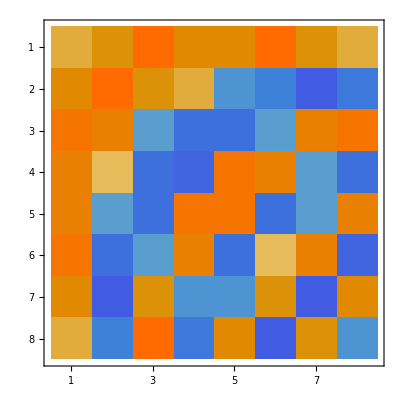

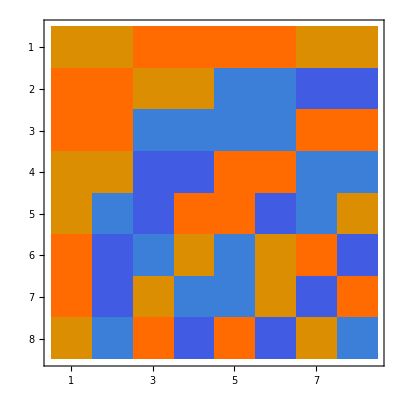

```mathematica
(* matrice de passage de la base des 4-molécules vers la base de la 8-molécule *)
pass8=Transpose[{ppp,ppm,pmp,pmm,mpp,mpm,mmp,mmm}];
MatrixPlot[pass8/.numeric];
MatrixPlot[pass44.pass8/.numeric]
MatrixPlot[pass44.pass8/.t2->0/.numeric]
```

#### Matrice de Parisi

```mathematica
parisi4={{0,t0,t1/2,t1/2},{t0,0,t1/2,t1/2},{t1/2,t1/2,0,t0},{t1/2,t1/2,t0,0}};
Eigensystem[parisi4]
```

{{-t0,-t0,t0-t1,t0+t1},{{0,0,-1,1},{-1,1,0,0},{-1,-1,1,1},{1,1,1,1}}}

```mathematica
t24=ConstantArray[t2/4,{4,4}];
parisi8=ArrayFlatten[{{parisi4,t24},{t24,parisi4}}];
%//MatrixForm;
Eigensystem[parisi8]
```

{{-t0,-t0,-t0,-t0,t0-t1,t0-t1,t0+t1-t2,t0+t1+t2},{{0,0,0,0,0,0,-1,1},{0,0,0,0,-1,1,0,0},{0,0,-1,1,0,0,0,0},{-1,1,0,0,0,0,0,0},{0,0,0,0,-1,-1,1,1},{-1,-1,1,1,0,0,0,0},{-1,-1,-1,-1,1,1,1,1},{1,1,1,1,1,1,1,1}}}

#### 16-molécule, à l’ordre t_3

```mathematica
SparseArray[{{1,2}->t0,{2,3}->t1,{3,4}->t0,{4,5}->t2,{5,6}->t0,{6,7}->t1,{7,8}->t0,{8,9}->t3,{9,10}->t0,{10,11}->t1,{11,12}->t0,{12,13}->t2,{13,14}->t0,{14,15}->t1,{15,16}->t0},{16,16}];
M16=%+Transpose[%];
M16//MatrixForm;
```

```mathematica
(* matrice de passage des 4-molécules vers la 8-molécule *)
pass8={ppp,ppm,pmp,pmm,mpp,mpm,mmp,mmm};
Series[pass8.pass44.M8.Transpose[pass8.pass44],{t1,0,1},{t2,0,1}]//Normal//Expand;
%/.t1 t2->0//MatrixForm
(* matrice de passage des atomes vers la 8-molécule *)
pass8at=pass8.pass44;
```

(t0+t1/2+t2/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | t0+t1/2-t2/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | t0-t1/2+t2/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | t0-t1/2-t2/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -t0+t1/2+t2/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -t0+t1/2-t2/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -t0-t1/2+t2/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -t0-t1/2-t2/4)

```mathematica
zero8=ConstantArray[0,{8,8}];
pass88=ArrayFlatten[{{pass8at,zero8},{zero8,pass8at}}];
%//MatrixForm;
```

```mathematica
pass88.M16.Transpose[pass88];
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
M88=%/.{t1 t2->0,t2 t3->0,t1 t3->0};
M88//MatrixForm;
```

#### Vecteurs propres de la 16-molécule

```mathematica
pppp={1,-t3/(4t2),t3/(8t1),-t3/(8t1),t3/(16t0),-t3/(16t0),t3/(16t0),-t3/(16t0),1,t3/(4t2),t3/(8t1),t3/(8t1),t3/(16t0),t3/(16t0),t3/(16t0),t3/(16t0)};
(t0+t1/2+t2/4+t3/8)^-1 M88.pppp;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==pppp
```

True

```mathematica
pppm={1,t3/(4t2),-t3/(8 t1),t3/(8 t1),-t3/(16t0),t3/(16t0),-t3/(16t0),t3/(16t0),-1,t3/(4t2),t3/(8 t1),t3/(8 t1),t3/(16t0),t3/(16t0),t3/(16t0),t3/(16t0)};
(t0+t1/2+t2/4-t3/8)^-1 M88.pppm;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==pppm
```

True

```mathematica
ppmp={t3/(4t2),1,-t3/(8t1) ,t3/(8 t1),-t3/(16 t0),t3/(16 t0),-t3/(16 t0),t3/(16 t0),t3/(4t2),-1,-t3/(8t1),-t3/(8 t1),-t3/(16 t0),-t3/(16 t0),-t3/(16 t0),-t3/(16 t0)};
(t0+t1/2-t2/4+t3/8)^-1 M88.ppmp;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==ppmp
```

True

```mathematica
ppmm={-t3/(4t2),1,t3/(8t1) ,-t3/(8 t1),t3/(16 t0),-t3/(16 t0),t3/(16 t0),-t3/(16 t0),t3/(4t2),1,-t3/(8t1),-t3/(8 t1),-t3/(16 t0),-t3/(16 t0),-t3/(16 t0),-t3/(16 t0)};
(t0+t1/2-t2/4-t3/8)^-1 M88.ppmm;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==ppmm
```

True

```mathematica
pmpp={-t3/(8t1),t3/(8t1),1 ,-t3/(4t2),t3/(16 t0),-t3/(16 t0),t3/(16 t0),-t3/(16 t0),-t3/(8t1),-t3/(8t1),1,t3/(4t2),t3/(16 t0),t3/(16 t0),t3/(16 t0),t3/(16 t0)};
(t0-t1/2+t2/4+t3/8)^-1 M88.pmpp;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==pmpp
```

True

```mathematica
pmpm={t3/(8t1),-t3/(8t1),1 ,t3/(4t2),-t3/(16 t0),t3/(16 t0),-t3/(16 t0),t3/(16 t0),-t3/(8t1),-t3/(8t1),-1,t3/(4t2),t3/(16 t0),t3/(16 t0),t3/(16 t0),t3/(16 t0)};
(t0-t1/2+t2/4-t3/8)^-1 M88.pmpm;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==pmpm
```

True

```mathematica
pmmm={-t3/(8t1),t3/(8t1),-t3/(4t2),1,t3/(16 t0),-t3/(16 t0),t3/(16 t0),-t3/(16 t0),t3/(8t1),t3/(8t1),t3/(4t2),1,-t3/(16 t0),-t3/(16 t0),-t3/(16 t0),-t3/(16 t0)};
(t0-t1/2-t2/4-t3/8)^-1 M88.pmmm;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==pmmm
```

True

```mathematica
pmmp={t3/(8t1),-t3/(8t1),t3/(4t2),1,-t3/(16 t0),t3/(16 t0),-t3/(16 t0),t3/(16 t0),t3/(8t1),t3/(8t1),t3/(4t2),-1,-t3/(16 t0),-t3/(16 t0),-t3/(16 t0),-t3/(16 t0)};
(t0-t1/2-t2/4+t3/8)^-1 M88.pmmp;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==pmmp
```

True

```mathematica
mppp={-t3/(16t0),t3/(16t0),-t3/(16t0),t3/(16t0),1,-t3/(4t2),t3/(8t1),-t3/(8t1),-t3/(16t0),-t3/(16t0),-t3/(16t0),-t3/(16t0),1,t3/(4t2),t3/(8t1),t3/(8t1)};
(-t0+t1/2+t2/4+t3/8)^-1 M88.mppp;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==mppp
```

True

```mathematica
mppm={t3/(16t0),-t3/(16t0),t3/(16t0),-t3/(16t0),1,t3/(4t2),-t3/(8t1),t3/(8t1),-t3/(16t0),-t3/(16t0),-t3/(16t0),-t3/(16t0),-1,t3/(4t2),t3/(8t1),t3/(8t1)};
(-t0+t1/2+t2/4-t3/8)^-1 M88.mppm;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==mppm
```

True

```mathematica
mpmp={t3/(16t0),-t3/(16t0),t3/(16t0),-t3/(16t0),t3/(4t2),1,-t3/(8t1),t3/(8t1),t3/(16t0),t3/(16t0),t3/(16t0),t3/(16t0),t3/(4t2),-1,-t3/(8t1),-t3/(8t1)};
(-t0+t1/2-t2/4+t3/8)^-1 M88.mpmp;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==mpmp
```

True

```mathematica
mpmm={-t3/(16t0),t3/(16t0),-t3/(16t0),t3/(16t0),-t3/(4t2),1,t3/(8t1),-t3/(8t1),t3/(16t0),t3/(16t0),t3/(16t0),t3/(16t0),t3/(4t2),1,-t3/(8t1),-t3/(8t1)};
(-t0+t1/2-t2/4-t3/8)^-1 M88.mpmm;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==mpmm
```

True

```mathematica
mmpp={-t3/(16t0),t3/(16t0),-t3/(16t0),t3/(16t0),-t3/(8t1),t3/(8t1),1,-t3/(4t2),-t3/(16t0),-t3/(16t0),-t3/(16t0),-t3/(16t0),-t3/(8t1),-t3/(8t1),1,t3/(4t2)};
(-t0-t1/2+t2/4+t3/8)^-1 M88.mmpp;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==mmpp
```

True

```mathematica
mmpm={t3/(16t0),-t3/(16t0),t3/(16t0),-t3/(16t0),t3/(8t1),-t3/(8t1),1,t3/(4t2),-t3/(16t0),-t3/(16t0),-t3/(16t0),-t3/(16t0),-t3/(8t1),-t3/(8t1),-1,t3/(4t2)};
(-t0-t1/2+t2/4-t3/8)^-1 M88.mmpm;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==mmpm
```

True

```mathematica
mmmp={t3/(16t0),-t3/(16t0),t3/(16t0),-t3/(16t0),t3/(8t1),-t3/(8t1),t3/(4t2),1,t3/(16t0),t3/(16t0),t3/(16t0),t3/(16t0),t3/(8t1),t3/(8t1),t3/(4t2),-1};
(-t0-t1/2-t2/4+t3/8)^-1 M88.mmmp;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==mmmp
```

True

```mathematica
mmmm={-t3/(16t0),t3/(16t0),-t3/(16t0),t3/(16t0),-t3/(8t1),t3/(8t1),-t3/(4t2),1,t3/(16t0),t3/(16t0),t3/(16t0),t3/(16t0),t3/(8t1),t3/(8t1),t3/(4t2),1};
(-t0-t1/2-t2/4-t3/8)^-1 M88.mmmm;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.{t1 t2->0,t2 t3->0,t1 t3->0};
%==mmmm
```

True

#### Vecteurs propres de la 16-molécule dans la base atomique

```mathematica
(* approximation supplémentaire *)
approx={t3/t0->0,t3/t1->0,t2/t0->0};
smplf={t1 t2->0,t2 t3->0,t1 t3->0};
(* numérique *)
Clear[α];
num={t3->α^3 t0, t2->α^2 t0, t1->α t0};
```

```mathematica
Transpose[pass88].mmpp;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
2 √2%//Expand;
%/.smplf/.approx/.num;
Manipulate[ListPlot[%,Filling->Axis,PlotStyle->PointSize[Medium],PlotRange->{-1.5,1.5}],{α,0,1}]
```

```mathematica
(* matrice de passage de la base des 2 8-molécules vers la base de la 16-molécule *)
Clear[pass8816];
pass8816=1/(√2){pppp,pppm,ppmp,ppmm,pmpp,pmpm,pmmp,pmmm,mppp,mppm,mpmp,mpmm,mmpp,mmpm,mmmp,mmmm};
Transpose[pass8816].pass8816;
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal;
%//MatrixForm;
```

```mathematica
pass8816.M88.Transpose[pass8816];
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
%/.smplf//MatrixForm;
```

```mathematica
Transpose[pass8816.pass88];
Series[%,{t1,0,1},{t2,0,1},{t3,0,1}]//Normal//Expand;
4%//Expand;
%/.smplf/.approx/.num;
glist=ListPlot[#/.α->0,Filling->Axis,PlotStyle->PointSize[Medium],PlotRange->{-1.5,1.5},Axes->True]&/@%;
```

```mathematica
Block[{plot,dir=NotebookDirectory[]<>"data/"},
plot=GraphicsRow[glist[[3;;5]],ImageSize->Large];
Export[dir<>"eigenfunctions_zeroth_order.pdf",plot]
]
```

/home/nicolas/git/spectrum_quasicrystals/hierarchical chain/data/eigenfunctions_zeroth_order.pdf